```mathematica
(*Cèsar Muro Cabral*)
```

## Execute this line.

```mathematica
Needs["FourierSeries`"];
```

# Study of electromagnetically induced transparency and light propation on ensembles of Rubidium 87 cold atoms in the D2 line .

## Three level system.

We start with the three level model . We construct and solve the Bloch equations from the density matrix approach to obtain the susceptibility.  Then we plot the absorption and dispersion

```mathematica
MatrixForm[sys3={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}}];
MatrixForm[h7={{0,0,ΩP/2},{0,Δp-Δc,ΩC/2},{ΩP/2,ΩC/2,Δp}}];
TableForm[dt1=-{{0,0,0},{0,γ21,0},{0,0,Γ/2}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3];
solg3=Simplify[Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, 21],leqs3[[3,1]]==-I*ω*Subscript[ρ, 31],χ3==Simplify[(Subscript[ρ, 31]/ΩP)]},{Subscript[ρ, 21],Subscript[ρ, 31],χ3}]/.{Subscript[ρ, 23]->0,Subscript[ρ, 33]->0,Subscript[ρ, 11]->1}];
χ3d=χ3/.solg3[[1]]
```

(2 (ⅈ γ21-Δc+Δp+ω))/(4 Δc Δp-4 Δp^2+2 Γ (γ21+ⅈ (Δc-Δp-ω))+4 Δc ω-8 Δp ω-4 ω^2-4 ⅈ γ21 (Δp+ω)+ΩC^2)

where Ωc is the control field, Δc,Δp are the detunings of the control and probe field, γ21=0.5Γ is the optical decoherence, and γ21=0.001Γ is the dephasing rate between the ground states. Therefore, from the previous result, we define the susceptibility

```mathematica
χΛ[ΩC_]:=(2 (ⅈ γ21-Δc+Δp+ω))/(4 Δc Δp-4 Δp^2+2 Γ (γ21+ⅈ (Δc-Δp-ω))+4 Δc ω-8 Δp ω-4 ω^2-4 ⅈ γ21 (Δp+ω)+ΩC^2)
```

And plot the absorption by employing the imaginary part of the susceptibility. Notice that as we increase the control field, we get a wider window of transparency, and when ΩC=0, then there is absorption

```mathematica
Manipulate[Plot[Im[χΛ[ΩC]/.{Γ->6.065,Δc->0,ω->0,γ21->0.001*6.065}],{Δp,-50,50},Frame->True,PlotRange->All,FrameLabel->{"δp(MHz)","Absorption Im χ"},Axes->False], {{ΩC,0,"Control field frequency"},0,40,5,Appearance->"Labeled"},SynchronousInitialization->False, SynchronousUpdating->False]
```

Now we plot the dispersion to see the effect of “slow light”

```mathematica
Manipulate[Plot[Re[χΛ[ΩC]/.{Γ->6.065,Δc->0,ω->0,γ21->0.001*6.065}],{Δp,-50,50},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"δp(MHz)","Dispersion Re χ"}], {{ΩC,0,"Control field frequency"},0,40,5,Appearance->"Labeled"},SynchronousInitialization->False, SynchronousUpdating->False]
```

## Four - level system (off resonant interaction)

Now, we consider that the atoms are pumped to the Zeeman sublevel F=1,m = 1. The control field is attached  is attached to the transition F=2,m=1→F’=2,m=2, with σ+ polarization, whereas the probe field to F=1,m=1→F’=2,m=2, with also σ+ polarization. In this four-level model,  we consider an off resonance interaction of the control field with the level F’=3,m=2. The hyperfine splitting between F’=2 and F’=1 is 266.65 MHz. Regarding the light propagation, we employ an initial Gaussian pulse with a temporal width of Tp=500ns.  Moreover, we write the Rabi frequency Rabi control in terms of the optical depth OD, i.e. Rabi=√((OD*Γ)/(ζ*Tp)). We obtain and solve the Bloch equations, plot the absorption Im[χ], the dispersion Re[χ] and the transmission with an optical depth of OD=275:

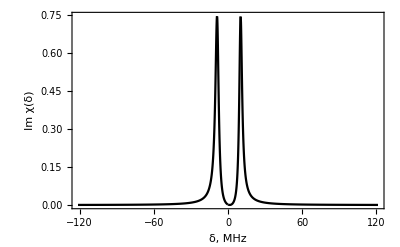

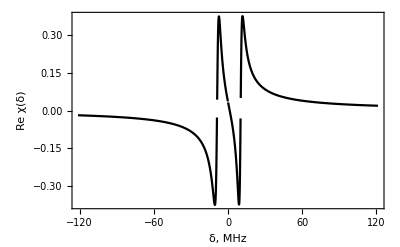

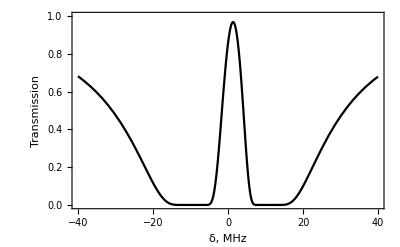

```mathematica
Γ=6.065;
j=3/2;
S=1/2;
IS=3/2;
hbar=1;
m=2;
γ21=0.0001*Γ;
hpf32=266.65;
γ31=0.5*Γ;
γ41=0.5*Γ;
OD=Table[OD=od ;OD,{od,0.00001,600,4}];
L001=Length[OD];
Tp=0.500;
ζ=2.0;
hbar=1;
Rabi=√((OD*Γ)/(ζ*Tp));
(*Probe field*)
Vp[Fe_,me_,Fg_,mg_]:=√(3/4*hbar*(2*j+1)*(2*Fg+1))*ClebschGordan[{Fg,mg},{1,me-mg},{Fe,me}]*SixJSymbol[{S,IS,Fg},{Fe,1,j}]*√Γ;
(*Control field, the dipole moment is obtained from the transtion strength, which is normalized respect to F=1,m=1->F'=2,m=2*)

Vc[Fe_,me_,Fs_,ms_]:=((ClebschGordan[{Fs,ms},{1,me-ms},{Fe,me}]*SixJSymbol[{S,IS,Fs},{Fe,1,j}])/(ClebschGordan[{2,1},{1,1},{2,2}]*SixJSymbol[{S,IS,Fs},{2,1,j}]))*Rabi/2;
MatrixForm[sys3={{Subscript[ρ, g3g3],Subscript[ρ, g3s3],Subscript[ρ, g3e4],Subscript[ρ, g3e5]},{Subscript[ρ, s3g3],Subscript[ρ, s3s3],Subscript[ρ, s3e4],Subscript[ρ, s3e5]},{Subscript[ρ, e4g3],Subscript[ρ, e4s3],Subscript[ρ, e4e4],Subscript[ρ, e4e5]},{Subscript[ρ, e5g3],Subscript[ρ, e5s3],Subscript[ρ, e5e4],Subscript[ρ, e5e5]}}];
MatrixForm[h7={{0,0,Subscript[ΩP, g3e4],0},{0,-Δc+Δp,Subscript[ΩC, s3e4],Subscript[ΩC, s3e5]},{Subscript[ΩP, g3e4],Subscript[ΩC, s3e4],+Δp,0},{0,Subscript[ΩC, s3e5],0,hpf32-Δc+Δp}}];
TableForm[dt1={{0,0,0,0},{0,γ21,0,0},{0,0,γ31,0},{0,0,0,γ41}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3];
solg3=Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, s3g3],leqs3[[3,1]]==-I*ω*Subscript[ρ, e4g3],leqs3[[4,1]]==-I*ω*Subscript[ρ, e5g3],Subscript[χ, g4l]==-Simplify[(Subscript[ρ, e4g3]*Subscript[ΩP, g3e4])]},{Subscript[ρ, s3g3],Subscript[ρ, e4g3],Subscript[ρ, e5g3],Subscript[χ, g4l]}]/.{Subscript[ρ, s3e4]->0,Subscript[ρ, e4e4]->0,Subscript[ρ, e5s3]->0,Subscript[ρ, e5e4]->0,Subscript[ρ, g3g3]->1};
Subscript[χ, pol4l]=Chop@Subscript[χ, g4l]/.solg3/.{Subscript[ΩC, s3e4]->Vc[2,2,2,1],Subscript[ΩC, s3e5]->Vc[3,2,2,1],Subscript[ΩP, g3e4]->Vp[2,2,1,1]};

Plot[{Evaluate[Im[Subscript[χ, pol4l][[1]][[16]]]/.{Δc->0,ω->0}]},{Δp,-20*Γ,20*Γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->TraditionalForm/@{"δ, MHz","Im χ(δ)"}]
Plot[{Evaluate[Re[Subscript[χ, pol4l][[1]][[16]]]/.{Δc->0,ω->0}]},{Δp,-20*Γ,20*Γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,Frame->True,Axes->False,FrameLabel->TraditionalForm/@{"δ, MHz","Re χ(δ)"}]

Plot[Exp[-((Γ/2)*OD[[16]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[16]]/.{Δc->0,ω->0})]]],{Δp,-40,40},PlotStyle->Black,PlotRange->{0,1.0},Frame->True,Frame->True,Axes->False,FrameLabel->TraditionalForm/@{"δ, MHz","Transmission"}]
```

Now we construct a table called “det”, with the detunings  Δp’s where the transmission achieves the maximum for each optical depth.

```mathematica
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]])*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ΔD->0,ω->0})]]],0<=Δp<=15},{Δp,-1}]],{i,1,L001}]
```

{10.2926,0.090897,0.181685,0.272366,0.362939,0.453406,0.543765,0.634019,0.724167,0.814209,0.904146,0.993979,1.08371,1.17333,1.26285,1.35227,1.44158,1.5308,1.61991,1.70892,1.79782,1.88663,1.97533,2.06394,2.15244,2.24085,2.32915,2.41736,2.50547,2.59348,2.68139,2.76921,2.85692,2.94454,3.03207,3.11949,3.20683,3.29406,3.3812,3.46825,3.5552,3.64205,3.72881,3.81548,3.90206,3.98854,4.07493,4.16122,4.24743,4.33354,4.41956,4.50549,4.59133,4.67708,4.76273,4.8483,4.93378,5.01916,5.10446,5.18967,5.27479,5.35982,5.44477,5.52962,5.61439,5.69907,5.78367,5.86817,5.95259,6.03693,6.12118,6.20534,6.28942,6.37341,6.45732,6.54114,6.62488,6.70853,6.7921,6.87559,6.959,7.04232,7.12555,7.20871,7.29178,7.37477,7.45768,7.54051,7.62326,7.70592,7.78851,7.87101,7.95343,8.03578,8.11804,8.20023,8.28233,8.36436,8.4463,8.52817,8.60996,8.69167,8.7733,8.85486,8.93634,9.01774,9.09906,9.18031,9.26148,9.34257,9.42359,9.50453,9.5854,9.66619,9.7469,9.82754,9.90811,9.9886,10.069,10.1494,10.2296,10.3098,10.3899,10.47,10.55,10.6299,10.7097,10.7894,10.8691,10.9487,11.0283,11.1077,11.1871,11.2665,11.3457,11.4249,11.504,11.5831,11.662,11.7409,11.8198,11.8985,11.9772,12.0558,12.1344,12.2129,12.2913,12.3696,12.4479,12.5261}

We write the inital Gaussian pulse as Wp0[ω]= Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])]. To compute the optical storage-efficiency, we analyze two equivalent approaches: -integrating in ω-frequency domain and 
- numerical Fourier transform. 
We construct the output pulse at the end of the ensmeble  as ϵ_out=Wp0[ω]*Exp[-((Γ/2)*OD[[i]]/(Vp[4,4,3,3]^2))*Evaluate[Im[(χ_pol4l[[1]][[i]]/.{Δc→0,Δp->det[[i]]})]]], and the efficiency of the optical memory is estimated as (∫_(-∞)^∞ |ϵ_out|^2 ⅆω)/(∫_(-∞)^∞ |ϵ_in|^2 ⅆω) , and  (∫_(-∞)^∞ |ϵ_out|^2 ⅆt)/(∫_(-∞)^∞ |ϵ_in|^2 ⅆt).Therefore

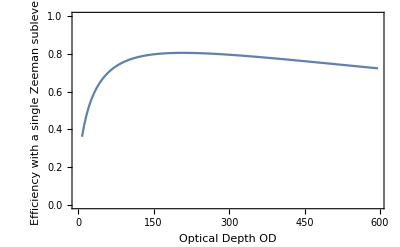

```mathematica
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=15},{Δp,1}]],{i,1,L001}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
(*I store the out pulse in a table being every element the corresponding for for every optical depth*)
ϵ3d2out=Table[Wp0[ω]*Exp[-((Γ/4)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,Δp->det[[i]]})]]],{i,1,L001}];
(*Then I follow the formula (14) for the the slow light transmission efficiency  "Broadband coherent optical memory"*)
eff4l=Table[NIntegrate[Abs[ϵ3d2out[[i]]]^2,{ω,-∞,∞}]/NIntegrate[Abs[Wp0[ω]]^2,{ω,-∞,∞}],{i,1,L001}];
data4l=Transpose@{OD,eff4l};
(*As you can see large optical depth*)
ListPlot[Delete[data4l,{{1},{2}}],Frame->True,PlotRange->{All,{0,1.0}},Joined->True,FrameLabel->{"Optical Depth OD","Efficiency with a single Zeeman sublevel"}]
```

Numerical Fourier Transform function throught Mathematica function NInverseFourier transform. We have to run the first line of the code. The time interval where we calculate the Fourier transform (thus the efficiency) is from -6 to 6, in steps size of 0.25.

```mathematica
τ=Table[τ=tim;τ,{tim,-6,6,0.25}];
OD=Table[OD=od ;OD,{od,0.00001,600,4}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
L001=Length[OD];
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=35},{Δp,1}]],{i,1,L001}];

ϵ3d2out=Table[Wp0[ω]*Exp[-((Γ/4)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,Δp->det[[i]]})]]],{i,1,L001}];
ft4l=Table[Chop@NInverseFourierTransform[ϵ3d2out[[h]],ω,i],{h,2,L001},{i,-6,6,.25}];
```

$Aborted

```mathematica
ϵsZ=Transpose@{Delete[OD,{{1}}],Chop@Table[NIntegrate[(Interpolation[Transpose@{τ,ft4l[[i]]},InterpolationOrder->3][t])^2,{t,-8,8}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ft4l]}]}
ListPlot[{Delete[data4l,{{1},{2}}],Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18]]
```

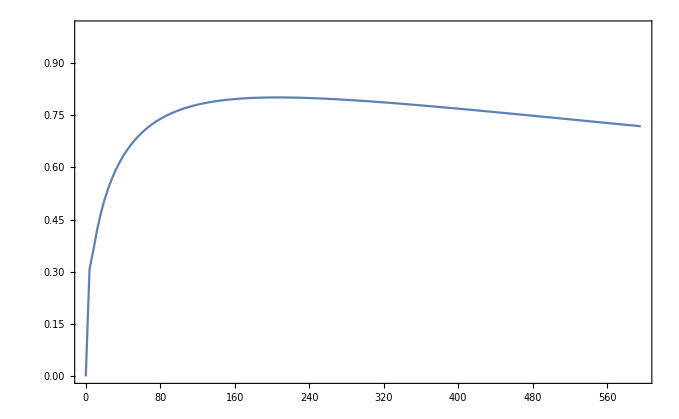

```mathematica
ListPlot[{Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18],PlotRangePadding->None]
```

We observe that the efficiency achieves a maximum of 80% around an optical depth of 140, after that,  it tends to decrease slowly.